# VE401 Recitation 7

## Simple Linear Regression

Example: We want to do physical experiment to measure the gravitational acceleration g≈9.8 m/s^2. We have several weights of 10g each. We use springs to measure their gravitational forces:

```mathematica
X={10,20,30,40,50,60,70,80};
```

```mathematica
Residual=RandomVariate[NormalDistribution[0,0.05],Length[X]]
```

{-0.0115325,0.0157878,0.0294766,-0.0597483,0.0173925,0.0349411,0.0903353,0.122338}

```mathematica
Y=0.0098*X+Residual
```

{0.0864675,0.211788,0.323477,0.332252,0.507393,0.622941,0.776335,0.906338}

```mathematica
Data=Transpose[{X,Y}]
```

{{10,0.0864675},{20,0.211788},{30,0.323477},{40,0.332252},{50,0.507393},{60,0.622941},{70,0.776335},{80,0.906338}}

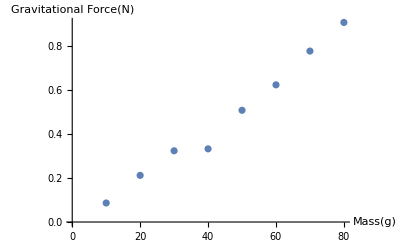

```mathematica
ListPlot[Data,AxesLabel->{"Mass(g)","Gravitational Force(N)"}]
```

### Setting and Assumptions

Setting: we have

An independent variable X, or predictor variable or regressor,

A dependent variable Y, or a response variable.

Assumptions:

Y is approximately linearly dependent on X, Y_i=β_0+β_1 x_i+E_i for some β_0,β_1∈ℝ for all x.

The error term E_i follows a normal distribution with mean 0 and variance σ^2. This means that Y|x is also normal with variance σ^2 and mean μ_(Y|x)=β_0+β_1 x.

If my spring has more variance when the mass is large, the data may look like:

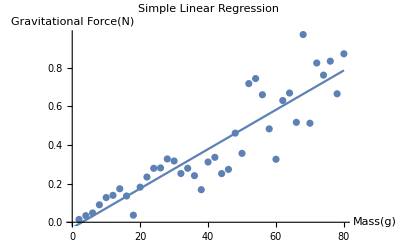

```mathematica
Xalt=Range[40]*2;
Yalt=Table[0.0098*x+RandomVariate[NormalDistribution[0,0.003*x]],{x,Xalt}];
DataAlt=Transpose[{Xalt,Yalt}];
lmAlt=LinearModelFit[DataAlt,m,m];
Show[ListPlot[DataAlt],Plot[lmAlt[x],{x,0,80}],PlotLabel->"Simple Linear Regression",AxesLabel->{"Mass(g)","Gravitational Force(N)"}]
```

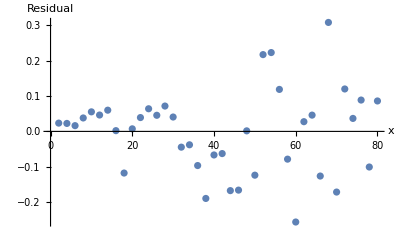

```mathematica
ListPlot[Transpose[{Xalt,lmAlt["FitResiduals"]}],AxesLabel->{"x","Residual"}]
```

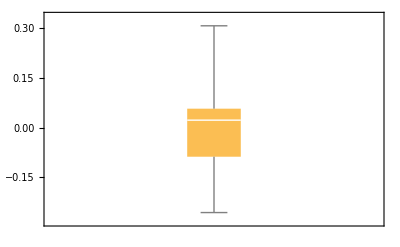

```mathematica
BoxWhiskerChart[lmAlt["FitResiduals"]]
```

If the spring has wrong labels, the data may look like:

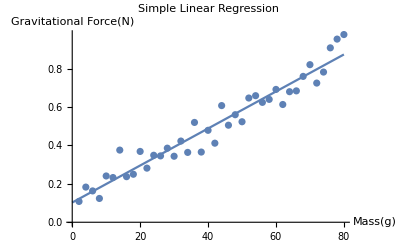

```mathematica
XMov=Range[40]*2;
YMov=Table[0.0098*x+RandomVariate[NormalDistribution[0.1,0.05]],{x,XMov}];
DataMov=Transpose[{XMov,YMov}];
lmMov=LinearModelFit[DataMov,m,m];
Show[ListPlot[DataMov],Plot[lmMov[x],{x,0,80}],PlotLabel->"Simple Linear Regression",AxesLabel->{"Mass(g)","Gravitational Force(N)"}]
```

```mathematica
lmMov
```

FittedModel[0.10274+0.00963947 m]

Y|x_i and Y|x_j are independent if x_i≠x_j.

### Least-Squares Estimation

Intuition: we want to find b_0 and b_1 such that SS_E:=∑_(i=1)^n (y_i-(b_0+b_1 x_i))^2=S_yy-b_1 S_xy is minimized.

Mathematical representation:

b_1=(n∑_(i=1)^n x_i y_i-(∑_(i=1)^n x_i)(∑_(i=1)^n y_i))/(n∑_(i=1)^n x_i^2-(∑_(i=1)^n x_i)^2)=(∑_(i=1)^n (x_i-x̄)(y_i-ȳ))/(∑_(i=1)^n (x_i-x̄)^2)=S_xy/S_xx                (point estimate of β_1=Cov[X,Y]/Var[X])
b_0=1/n∑_(i=1)^n y_i-b_1·1/n∑_(i=1)^n x_i=ȳ-b_1 x̄                                         (point estimate of β_0=E[Y]-β_1 E[X])

where

S_xx:=∑_(i=1)^n x_i^2-1/n(∑_(i=1)^n x_i)^2=∑_(i=1)^n (x_i-x̄)^2                                     (estimates (n-1)Var[X])
S_yy:=∑_(i=1)^n y_i^2-1/n(∑_(i=1)^n y_i)^2=∑_(i=1)^n (y_i-ȳ)^2                                     (estimates (n-1)Var[Y])
S_xy:=∑_(i=1)^n x_i y_i-(∑_(i=1)^n x_i)(∑_(i=1)^n y_i)=∑_(i=1)^n (x_i-x̄)(y_i-ȳ)        (estimates (n-1)Cov[X,Y])

```mathematica
Data
```

{{10,0.0864675},{20,0.211788},{30,0.323477},{40,0.332252},{50,0.507393},{60,0.622941},{70,0.776335},{80,0.906338}}

Example: For our data, we can calculate using the statistics function of Casio calculators

```mathematica
-Graphics--Graphics-
```

```mathematica
-Graphics--Graphics-
```

##### Calculate S_xx,S_yy and S_xy.

We have

```mathematica
Covariance[X,Y]*(8-1)
```

48.1768

S_xx:=∑_(i=1)^n x_i^2-1/n(∑_(i=1)^n x_i)^2=20400-1/8(360)^2=4200
S_yy:=∑_(i=1)^n y_i^2-1/n(∑_(i=1)^n y_i)^2=2.337-1/8(3.767)^2=0.5632
S_xy:=∑_(i=1)^n x_i y_i-1/n(∑_(i=1)^n x_i)(∑_(i=1)^n y_i)=217.69-1/8 360×3.767=48.177

##### Calculate the estimation of β_0 and β_1 of the model.

We have

b_1=(n∑_(i=1)^n x_i y_i-(∑_(i=1)^n x_i)(∑_(i=1)^n y_i))/(n∑_(i=1)^n x_i^2-(∑_(i=1)^n x_i)^2)=(8×217.69-360×3.77)/(8×20400-(360)^2)=0.0114
b_0=1/n∑_(i=1)^n y_i-b_1·1/n∑_(i=1)^n x_i=ȳ-b_1 x̄=0.47-0.0114×45=-0.043

which is fairly close to the true value of β_1=0.0098, β_0=0.

```mathematica
lm=LinearModelFit[Data,m,m]
```

FittedModel[-0.0453065+0.0114707 m]

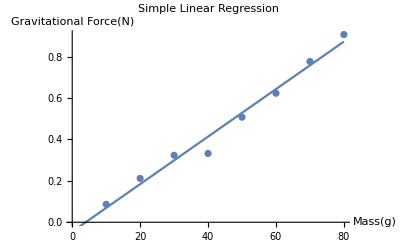

```mathematica
Show[ListPlot[Data],Plot[lm[x],{x,0,80}],PlotLabel->"Simple Linear Regression",AxesLabel->{"Mass(g)","Gravitational Force(N)"}]
```

The SS_E=S_yy-b_1 S_xy=0.5632-0.01147×48.177=0.0106.

```mathematica
Total[lm["FitResiduals"]^2]
```

0.010609

### Distribution of the Least Squares Estimator

Theorem:

Estimator | Distribution | Mean | Variance
B_1 (estimator of β_1) | Normal | β_1 | σ^2/S_xx
B_0 (estimator of β_0) | Normal | β_0 | σ^2 (∑_(i=1)^n x_i)/(n S_xx)

Important property: ∑_(i=1)^n (x_i-x̄)=0, ∑_(i=1)^n (x_i-x̄)^2=∑_(i=1)^n (x_i-x̄)x_i+x̄∑_(i=1)^n (x_i-x̄)=∑_(i=1)^n (x_i-x̄)x_i.

Proof: For B_1, we have

B_1=(∑_(i=1)^n (x_i-x̄)(Y_i-Ȳ))/(∑_(i=1)^n (x_i-x̄)^2)
=(∑_(i=1)^n (x_i-x̄)Y_i-Ȳ∑_(i=1)^n (x_i-x̄))/(∑_(i=1)^n (x_i-x̄)^2)
=(∑_(i=1)^n (x_i-x̄)Y_i)/(∑_(i=1)^n (x_i-x̄)^2)=∑_(i=1)^n (x_i-x̄)/(∑_(j=1)^n (x_j-x̄)^2)Y_i=:∑_(i=1)^n c_i Y_i

Therefore B_1 is a linear combination of i.i.d. normal distributed RV, so B_1 is normally distributed. furthermore,

B_1=(∑_(i=1)^n (x_i-x̄)(β_0+β_1 x_i+E_i))/(∑_(i=1)^n (x_i-x̄)^2)
=β_1 (∑_(i=1)^n (x_i-x̄)x_i)/(∑_(i=1)^n (x_i-x̄)^2)+(∑_(i=1)^n (x_i-x̄)E_i)/(∑_(i=1)^n (x_i-x̄)^2)
=β_1+(∑_(i=1)^n (x_i-x̄)E_i)/(∑_(i=1)^n (x_i-x̄)^2)

Therefore the expectation is given by

E[B_1]=β_1+E[(∑_(i=1)^n (x_i-x̄)E_i)/(∑_(i=1)^n (x_i-x̄)^2)]
=β_1+(∑_(i=1)^n (x_i-x̄)E[E_i])/(∑_(i=1)^n (x_i-x̄)^2)
=β_1

and

Var[B_1]=0+Var[(∑_(i=1)^n (x_i-x̄)E_i)/(∑_(i=1)^n (x_i-x̄)^2)]
=∑_(i=1)^n c_i^2 Var[E_i]
=∑_(i=1)^n ((x_i-x̄)/(∑_(j=1)^n (x_j-x̄)^2))^2 σ^2
=(∑_(i=1)^n (x_i-x̄)^2)/((∑_(j=1)^n (x_j-x̄)^2)^2)σ^2
=σ^2/(∑_(j=1)^n (x_j-x̄)^2)=σ^2/S_xx

##### Verify the same theorem for B_0=Ȳ-B_1 x̄.

For B_0, since B_0=Ȳ-B_1 x̄ and Ȳ=1/n∑_(i=1)^n Y_i=1/n∑_(i=1)^n (β_0+β_1 x_i+E_i)=β_0+β_1 1/n∑_(i=1)^n x_i+1/n∑_(i=1)^n E_i we have

E[B_0]=E[Ȳ]-x̄ E[B_1]
=β_0+β_1 x̄-β_1 x̄
=β_0

and

Var[B_0]=Var[Ȳ]+(x̄)^2 Var[B_1]
=σ^2/n+((σ^2(1/n∑_(i=1)^n x_i))^2)/S_xx
=σ^2(1/n+((1/n∑_(i=1)^n x_i)^2)/(∑_(i=1)^n x_i^2-1/n(∑_(i=1)^n x_i)^2))
=σ^2[1/n+(-1/n+(1/n∑_(i=1)^n x_i^2)/(∑_(i=1)^n x_i^2-1/n(∑_(i=1)^n x_i)^2))]
=σ^2 (∑_(i=1)^n x_i)/(n S_xx)

##### If the mean of error is not 0, are the estimators B_0,B_1 still unbiased?

They will no longer be unbiased.

##### If the variance of error is not constant, but the mean is 0, are the estimators B_0,B_1 still unbiased?

In this case they are still unbiased.

### Least Squares Estimator for the Variance

The variance σ^2 of Y|x can be estimated by

S^2:=SS_E/(n-2)=1/(n-2)∑_(i=1)^n (y_i-(b_0+b_1 x_i))^2

And

((n-2)S^2)/σ^2=SS_E/σ^2\[Distributed]χ_(n-2)^2

Using this we can calculate the 100(1-α)% confidence interval

B_1±t_(α/2,n-2) S/(√S_xx)           B_0±t_(α/2,n-2) (S √(∑_(i=1)^n x_i))/(√(n S_xx))

##### Calculate the confidence interval for the parameter of previous model.

We can calculate S^2=SS_E/(n-2)=0.106/6=0.0176.

```mathematica
lm["EstimatedVariance"]
```

0.00176817

```mathematica
lm["ParameterConfidenceIntervals", ConfidenceLevel->0.95]
```

{{-0.125479,0.0348662},{0.00988302,0.0130583}}

### Test for Significance of Regression

Testing Parameter |  Null Hypothesis | Test Statistics
β_1 | H_0:β_1=0 | T_(n-2)=B_1/(S/√S_xx)=R/(√(1-R^2))√(n-2) 
 |  |

We reject H_0 if T_(n-2)>t_(α/2,n-2).

##### Test the significance of regression of our previous model.

```mathematica
lm["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | -0.0453065 | 0.0327648 | -1.38278 | 0.215995
x | 0.0114707 | 0.00064884 | 17.6787 | 2.10336×10^-6

We conclude that there is NO evidence that the intercept is not 0, and there is evidence that the slope is not 0.

### Distribution of Estimated Mean (Predictor)

Estimator | Distribution | Mean | Variance
Ŷ|x (estimator of μ_(Y|x)) | Normal | μ_(Y|x) | σ √(1/n+(x-x̄)^2/S_xx)
Ŷ|x-Y|x | Normal | 0 | (1+1/n+(x-x̄)^2/S_xx)σ^2

The 100(1-α)% confidence interval for the conditional mean is

(μ̂)_(Y|x)±t_(α/2,n-2) S √(1/n+(x-x̄)^2/S_xx)

With 100(1-α)% chance, the conditional mean μ_(Y|x) will lie in this interval.

The 100(1-α)% prediction interval for the observed value is

(μ̂)_(Y|x)±t_(α/2,n-2) S √(1+1/n+(x-x̄)^2/S_xx)

With 100(1-α)% chance, the newly observed value Y|x_new will lie in this interval.

```mathematica
conf=lm["MeanPredictionBands",ConfidenceLevel->0.95];
pred=lm["SinglePredictionBands",ConfidenceLevel->0.95];
Show[ListPlot[Data],Plot[{lm[x],conf,pred},{x,0,80},PlotStyle->{Black,Red,Red,Blue,Blue},PlotLegends->Automatic],PlotLabel->"Simple Linear Regression",AxesLabel->{"Mass(g)","Gravitational Force(N)"}]
```

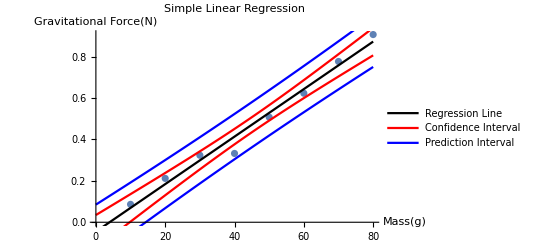

### R^2

Intuition: We want to see how much variance is explained by our model.

Mathematical representation: The total sum of squares SS_T=S_yy=∑_(i=1)^n (Y_i-Ȳ)^2, representing the variance of Y.

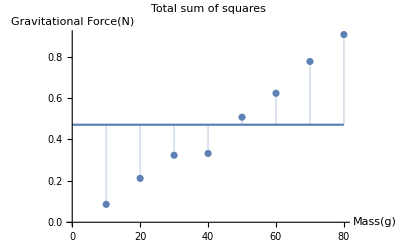

```mathematica
Show[ListPlot[Data,Filling->Mean[Y]],Plot[Mean[Y],{x,0,80},PlotLegends->"Ȳ"],PlotLabel->"Total sum of squares",AxesLabel->{"Mass(g)","Gravitational Force(N)"}]
```

The error sum of squares SS_E=∑_(i=1)^n (Y_i-(β_0+β_1 x))^2, representing the variance of Y that remains after applying the model.

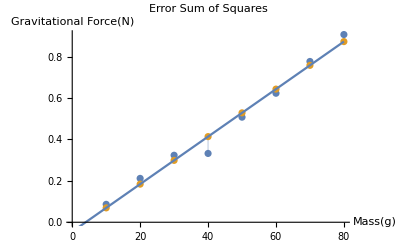

```mathematica
fit=0.0114707X-0.0453065;

Show[ListPlot[{Data,Transpose[{X,fit}]},Filling->{1->{2}}],Plot[lm[x],{x,0,80}],PlotLabel->"Error Sum of Squares",AxesLabel->{"Mass(g)","Gravitational Force(N)"}]
```

The correlation of determination is

R^2=(SS_T-SS_E)/SS_T=S_xy^2/(S_xx S_yy)

Note. R^2 is the square of the estimator of ρ_XY.

##### Calculate R^2 of our model.

The R^2 value of our model is S_xy^2/(S_xx S_yy)=48.177^2/(4200×0.5632)=0.9812

```mathematica
lm["RSquared"]
```

0.981164

### Testing for Lack of Fit

Testing Parameter |  Null Hypothesis | Test Statistics
SS_(E,lf) | H_0:the linear regression model is appropriate
(the error due to lack of fit is small) | F_(k-2,n-k)=(SS_(E,lf)/(k-2))/(SS_(E,pe)/(n-k)) 
 |  |

We reject H_0 if F_(k-2,n-k)>f_(α,k-2,n-k).

Example: We perform 4 more experiments to measure SS_(E,pe),

```mathematica
Xextra={10,40,60,70};
Yextra=0.0098*Xextra+RandomVariate[NormalDistribution[0,0.05],Length[Xextra]];
DataNew=Transpose[{Flatten[{X,Xextra}],Flatten[{Y,Yextra}]}]
```

{{10,0.0864675},{20,0.211788},{30,0.323477},{40,0.332252},{50,0.507393},{60,0.622941},{70,0.776335},{80,0.906338},{10,0.0412471},{40,0.409575},{60,0.54236},{70,0.544538}}

Steps:

Perform linear regression on the set of data,

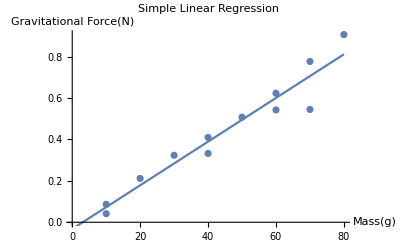

```mathematica
lmNew=LinearModelFit[DataNew,x,x];
Show[ListPlot[DataNew],Plot[lmNew[x],{x,0,80}],PlotLabel->"Simple Linear Regression",AxesLabel->{"Mass(g)","Gravitational Force(N)"}]
```

Identify that there are k distinct x values. In this case k=8.

```mathematica
lmNew
```

FittedModel[-0.0324704+0.0105451 x]

Calculate for the i^th group (i=1,...,k) of repeated x the internal sum of squares, ∑_(j=1)^n_i (Y_ij-(Ȳ)_i)^2.

For n=10,∑_(j=1)^2 (Y_(1,j)-(Ȳ)_1)^2=0.001
For n=40,∑_(j=1)^2 (Y_(2,j)-(Ȳ)_2)^2=0.003
For n=60,∑_(j=1)^2 (Y_(3,j)-(Ȳ)_3)^2=0.003
For n=70,∑_(j=1)^2 (Y_(4,j)-(Ȳ)_4)^2=0.027

Sum them up to get error sum of squares due to pure error. SS_(E,pe)/σ^2 follows a chi-squared distribution with n-k=12-8=4 degrees of freedom.

SS_(E,pe)=0.001+0.003+0.003+0.027=0.034

The sum of square error is calculated by

SS_E=S_yy-b_1 S_xy=0.052

```mathematica
Total[lmNew["FitResiduals"]^2]
```

0.0515848

The error due to lack of fit is

SS_(E,lf)=SS_E-SS_(E,pe)
=0.052-0.034
=0.018

SS_(E,lf)/σ^2 follows k-2=6 degree of freedom.

Calculate F statistics,

```mathematica
1-CDF[FRatioDistribution[6,4],(0.018/6)/(0.034/4)]
```

0.8771642274430168

There is no evidence that the linear model is not appropriate here.

## Multiple Linear Regression

### Settings and Assumptions

To discuss the model

Y|x=β_0+β_1 x_1+β_2 x_2+...+β_p x_p+E

We gives the same assumptions, and define

Y=(y_1
y_2
⋮
y_n),X=(1 | x_11 | ⋯ | x_p1
1 | x_12 |   |  
⋮ | ⋮ | ⋱ | ⋮
1 | x_(1n) |   | x_pn),β=(β_0
β_1
⋮
β_p),E=(e_1
e_2
⋮
e_n)

We have Y=X β+E.

### Least Squares Estimation

To minimize SS_E=(Y-X b)^T(Y-X b), we have b=(X^T X)^-1 X^T Y.

Example: I want to check whether gravitational force is related to the square of mass, so I fit my data to the model y=b_0+b_1 x+b_2 x^2. I calculate

```mathematica
y=Transpose[Data][[2]];
x=Transpose[Table[Function[x,x^k]/@Transpose[Data][[1]],{k,0,2}]];
{MatrixForm[x],MatrixForm[y]}
```

{(1 | 10 | 100
1 | 20 | 400
1 | 30 | 900
1 | 40 | 1600
1 | 50 | 2500
1 | 60 | 3600
1 | 70 | 4900
1 | 80 | 6400),(0.0864675
0.211788
0.323477
0.332252
0.507393
0.622941
0.776335
0.906338)}

```mathematica
b=Inverse[Transpose[x].x].Transpose[x].y;
MatrixForm[b]
```

(0.0350763
0.00664771
0.0000535885)

So the result become y=0.035+0.0066x+0.00005 x^2.

```mathematica
lmQuadratic=LinearModelFit[{x,y}]
```

FittedModel[0.0350763 #1+0.00664771 #2+0.0000535885 #3]

### Error Analysis

We define an orthogonal projection matrix

P=1/n(1 | 1 | ⋯ | 1
1 | 1 |   |  
⋮ | ⋮ | ⋱ | ⋮
1 | 1 |   | 1)

which can map a vector in ℝ^n to the mean of its entries. It has the nice property that P^2=P,P^T=P.

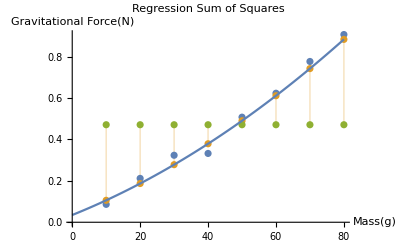

```mathematica
fit=0.035+0.0066X+0.00005 X^2;
repeat[m_,n_Integer?Positive]:=Sequence@@ConstantArray[m,n];
Show[ListPlot[{Data,Transpose[{X,fit}],Transpose[{X,{repeat[Mean[Y],Length[Data]]}}]},Filling->{2->{3}}],Plot[0.035+0.0066x+0.00005 x^2,{x,0,80}],PlotLabel->"Regression Sum of Squares",AxesLabel->{"Mass(g)","Gravitational Force(N)"}]
```

We can then write SS_T=⟨(𝟙_n-P)Y,(𝟙_n-P)Y⟩=⟨Y,(𝟙_n-P)Y⟩. Furthermore, we define the hat matrix H=(X(X^T X))^-1 X^T, then Ŷ=X b=(X(X^T X))^-1 X^T Y=H Y.

SS_T=∑_(i=1)^n (Y_i-Ȳ)^2=⟨Y,(𝟙_n-P)Y⟩
=⟨Y,(𝟙_n-H)Y⟩+⟨Y,(H-P)Y⟩
=SS_E+SS_R
=∑_(i=1)^n (Y_i-(Ŷ)_i)^2+∑_(i=1)^n ((Ŷ)_i-Ȳ)^2

where SS_R is the regression sum of squares. Then the coefficient of multiple determination is

R^2=(SS_T-SS_E)/SS_T=SS_R/SS_T

```mathematica
lm["RSquared"]
```

0.981164

```mathematica
lmQuadratic["RSquared"]
```

0.98973

### Distribution of Sum of Squares Error

SS_E/σ^2 follows a chi-squared distribution with n-p-1 degrees of freedom.

If β_1=β_2=⋯=β_p=0, then SS_R/σ^2 follows a chi-squared distribution with p degrees of freedom.

SS_R and SS_E are independent.

The estimator for variance S^2=SS_E/(n-p-1) is unbiased.

```mathematica
lm["EstimatedVariance"]
```

0.00176817

```mathematica
lmQuadratic["EstimatedVariance"]
```

0.00115691

### F-test for significance of Regression

Testing Parameter |  Null Hypothesis | Test Statistics
β_1,β_2,...,β_p | H_0:β_1=β_2=⋯=β_p=0 | F_(p,n-p-1)=(SS_R/p)/(SS_E/(n-p-1)) 
 |  |

We reject H_0 if F_(p,n-p-1)>f_(α,p,n-p-1).

## R Demonstration

The R language is powerful and easy to use when doing regression analysis. See the VE401RC7_R_Demo folder.